# Простые числа и аппроксимация

```mathematica
(* ===== Section 1: Generate first 10 prime numbers ===== *)
(* Commands used: Do, If, IntegerQ, AppendTo, Complement *)

ClearAll["Global`*"];

primeList  = {};
candidates = {};

Do[
  AppendTo[candidates, n];
  divisors = {};
  Do[
    If[IntegerQ[n/k], AppendTo[divisors, k]],
    {k, 2, n - 1}
  ];
  (* Complement[divisors, {}] == {} <=> no proper divisors => n is prime *)
  If[Complement[divisors, {}] === {}, AppendTo[primeList, n]];
  If[Length[primeList] >= 10, Break[]],
  {n, 2, 100}
];

Print["First 10 primes: ", primeList]
```

First 10 primes: {2,3,5,7,11,13,17,19,23,29}

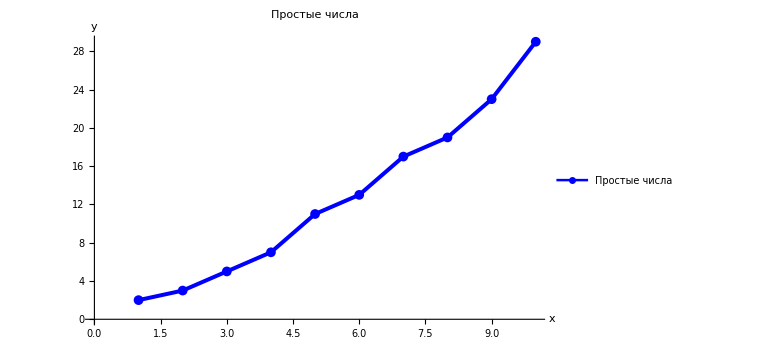

```mathematica
(* ===== Section 2: ListPlot with Joined ===== *)

xValues = Range[Length[primeList]];
points  = Transpose[{xValues, primeList}];

primePlot = ListPlot[
  points,
  Joined        -> True,
  PlotStyle     -> Directive[Blue, Thickness[0.005]],
  PlotMarkers   -> {Automatic, Medium},
  PlotLegends   -> Placed[{"Простые числа"}, {Right, Top}],
  PlotLabel     -> "Простые числа",
  AxesLabel     -> {"x", "y"},
  AxesOrigin    -> {0, 0},
  ImageSize     -> Large
]
```

Квадратичная аппроксимация: y = 0.566666666666678 + 1.0227272727272703*x + 0.17424242424242448*x^2

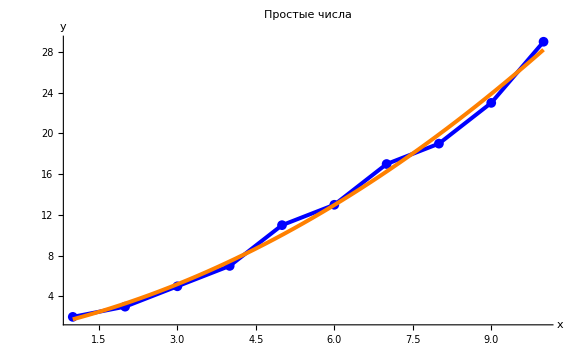

```mathematica
(* ===== Section 3: Quadratic LSM approximation ===== *)

fitModel = Fit[points, {1, x, x^2}, x];
Print["Квадратичная аппроксимация: y = ", fitModel // InputForm]

approxPlot = Plot[
  fitModel,
  {x, 1, 10},
  PlotStyle   -> Directive[Orange, Thickness[0.005]],
  PlotLegends -> Placed[{"Аппроксимация ряда простых чисел"}, {Right, Top}]
];

combinedPlot = Show[
  primePlot,
  approxPlot,
  PlotRange    -> All,
  ImagePadding -> 30
];

combinedPlot
```

```mathematica
(* ===== Section 4: Error computation: MSE, MAE, max error ===== *)
(* Using Table as required *)

approxValues = Table[fitModel /. x -> i, {i, xValues}];
errors       = N[primeList - approxValues];

maxError = Max[Abs[errors]];
n   = Length[primeList];
mse = N[(1/n) Total[errors^2]];
mae = N[(1/n) Total[Abs[errors]]];

Print["Сигма аппроксимации: ", N[approxValues]];
Print["Остатки (Yi - Yхат_i): ", errors];
Print["Max |error| = ", maxError // N];
Print["MSE = ", mse];
Print["MAE = ", mae]
```

Сигма аппроксимации: {1.76364,3.30909,5.20303,7.44545,10.0364,12.9758,16.2636,19.9,23.8848,28.2182}

Остатки (Yi - Yхат_i): {0.236364,-0.309091,-0.20303,-0.445455,0.963636,0.0242424,0.736364,-0.9,-0.884848,0.781818}

Max |error| = 0.963636

MSE = 0.406667

MAE = 0.548485

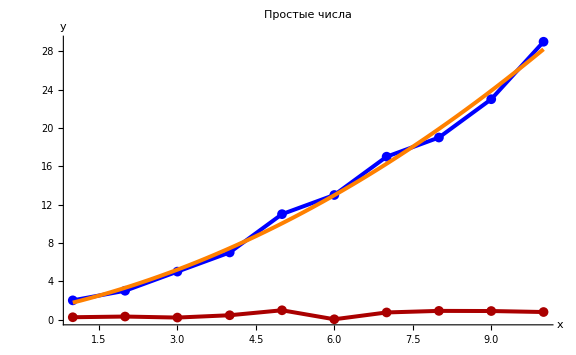

```mathematica
(* ===== Section 5: Figure 1 â.80.94 original data + approximation + error ===== *)

errorPoints = Transpose[{xValues, Abs[errors]}];
errorPlot = ListPlot[
  errorPoints,
  Joined      -> True,
  PlotStyle   -> Directive[Darker[Red], Thickness[0.005]],
  PlotMarkers -> {Automatic, Medium},
  PlotLegends -> Placed[{"Ошибка аппроксимации"}, {Right, Top}]
];

figure1 = Show[
  combinedPlot,
  errorPlot,
  PlotRange    -> All,
  PlotLabel    -> "Простые числа",
  AxesLabel    -> {"x", "y"},
  AxesOrigin   -> {0, 0},
  ImagePadding -> 30
];

figure1
```

```mathematica
(* ===== Section 6: Export figures and results ===== *)

outputDir = NotebookDirectory[];

Export[FileNameJoin[{outputDir, "combined_plot.png"}],      combinedPlot];
Export[FileNameJoin[{outputDir, "figure1_with_error.png"}], figure1];

reportText = StringRiffle[
  {
    "First 10 prime numbers: "      <> ToString[primeList],
    "Quadratic approximation: y = " <> ToString[fitModel // InputForm],
    "Approximation values: "        <> ToString[N[approxValues]],
    "Residuals (Yi - Yhat_i): "     <> ToString[errors],
    "Max absolute error: "          <> ToString[N[maxError]],
    "MSE = "                        <> ToString[mse],
    "MAE = "                        <> ToString[mae]
  },
  "\n"
];

Export[FileNameJoin[{outputDir, "lab2_results.txt"}], reportText, "Text"];
Print["Exported to ", outputDir]
```

Exported to /Users/justy-dev/Documents/University/Semester-6/Модели и методы анализа проектных решений/lab2/